# Unified neutrino definitions

This cell loads only the definitions from the adjacent TheorySpaceNeutrinos.wl. No tests, samples or plots run. StartHere.nb contains validation and usage examples.

```mathematica
Get[FileNameJoin[{NotebookDirectory[],"TheorySpaceNeutrinos.wl"}]];
```

## From Data

### Strong site

```mathematica
(*FIG.15:edit parameters here,then rerun the scan.Dimensional inputs are in TeV;use exact fractions.*)
```

```mathematica
fig15Parameters=Join[TSParameters["StrongSite","Local","Dirac","Boundary"],<|(*Graph and site disorder*)"Sites"->12,"SiteMean"->0,"SiteHalfWidth"->10,(*Uniform[-10,10]*)(*Hopping and distance suppression*)"HoppingMean"->1/10,"HoppingHalfWidth"->0,"DecayBase"->5,"EdgeLaw"->"Uniform",(*"Numerator":t/b^distance "NearestNeighbor":t/b^(distance-1),old l=t*b convention*)"DistanceNormalization"->"Numerator",(*Hamiltonian flavour matrix:identity for boundary mixing*)"HamiltonianFlavor"->IdentityMatrix[3],(*Left endpoint*)"ActiveCoupling"->173/1000,"ActiveFlavor"->IdentityMatrix[3],(*Right endpoint:Eq.(48) Yukawa texture*)"DiracRightCoupling"->173/1000,"DiracRightFlavor"->{{1,2/5,3/5},{3/10,1,4/5},{9/10,3/10,1}},(*Numerical settings*)"WorkingPrecision"->80,"MassOrdering"->"Ascending","Seed"->20261009|>];
```

```mathematica
fig15Parameters=Join[TSParameters["StrongSite","Local","Dirac","Hamiltonian"],<|(*Graph and site disorder*)"Sites"->12,"SiteMean"->0,"SiteHalfWidth"->10,(*Uniform[-10,10]*)(*Hopping and distance suppression*)"HoppingMean"->1/10,"HoppingHalfWidth"->0,"DecayBase"->5,"EdgeLaw"->"Uniform",(*"Numerator":t/b^distance "NearestNeighbor":t/b^(distance-1),old l=t*b convention*)"DistanceNormalization"->"Numerator",(*Hamiltonian flavour matrix:identity for boundary mixing*)"HamiltonianFlavor"->{{1,2/5,3/5},{3/10,1,4/5},{9/10,3/10,1}},(*Left endpoint*)"ActiveCoupling"->173/1000,"ActiveFlavor"->IdentityMatrix[3],(*Right endpoint:Eq.(48) Yukawa texture*)"DiracRightCoupling"->173/1000,"DiracRightFlavor"->IdentityMatrix[3],(*Numerical settings*)"WorkingPrecision"->80,"MassOrdering"->"Ascending","Seed"->20261009|>];
```

```mathematica
(*Sample count and plotting cut*)
fig15BatchSize=100;
fig15BatchCount=100;           (*10,000 trials,not 100,000*)
fig15ApplyRowCut=True;

(*Inspect everything before running.*)
Dataset[fig15Parameters]
```

```mathematica
(*STRONG-SITE DIRAC DATA GENERATION Three geometries and two flavour-mixing channels.Uses the numerical inputs in fig15Parameters.*)autoSummary=Module[{base=fig15Parameters,mixingMatrix,batchSize=100,batchCount=100,applyRowCut=True,cases,folder,summary={},geometry,channel,p,prefix,seconds,raw,dataFile,summaryFile,row,scanOK,j},If[!StringQ[NotebookDirectory[]],Print["Please save the notebook first."];
Return[$Failed]];
mixingMatrix={{1,2/5,3/5},{3/10,1,4/5},{9/10,3/10,1}};
cases=Tuples[{{"Local","Petersen","NonLocal"},{"Boundary","Hamiltonian"}}];
folder=CreateDirectory[FileNameJoin[{NotebookDirectory[],"PaperPlots_"<>DateString[{"Year","Month","Day","_","Hour","Minute","Second"}]}]];
Print["Saving strong-site Dirac data in: ",folder];
Do[{geometry,channel}=cases[[j]];
p=Join[base,<|"Preset"->"StrongSite","Nature"->"Dirac","Geometry"->geometry,"Channel"->channel,"ActiveFlavor"->IdentityMatrix[3],"HamiltonianFlavor"->If[channel==="Hamiltonian",mixingMatrix,IdentityMatrix[3]],"DiracRightFlavor"->If[channel==="Boundary",mixingMatrix,IdentityMatrix[3]]|>];
prefix=StringRiffle[{ToLowerCase[geometry],"site_strong",If[channel==="Boundary","yukawa","hamiltonian"],"dirac"},"_"];
Print["[",j,"/",Length[cases],"] Starting ",prefix," | ",batchSize batchCount," trials"];
{seconds,raw}=AbsoluteTiming[TSScan[p,batchSize batchCount,"Parallel"->True]];
(*Save every result before any selection or analysis.ApplyRowCut records the intended downstream selection.*)dataFile=Export[FileNameJoin[{folder,prefix<>"_data.wxf"}],<|"Parameters"->p,"BatchSize"->batchSize,"BatchCount"->batchCount,"ApplyRowCut"->applyRowCut,"Seconds"->seconds,"RawResults"->raw|>,"WXF"];
If[dataFile===$Failed,Print["Data saving failed. Stopping at ",prefix];
Return[<|"Folder"->folder,"CompletedCases"->summary,"UnsavedParameters"->p,"UnsavedRawResults"->raw|>]];
scanOK=ListQ[raw]&&Length[raw]==batchSize batchCount;
row=<|"Case"->prefix,"Parameters"->p,"Seconds"->seconds,"RecordCount"->If[ListQ[raw],Length[raw],0],"Status"->If[scanOK,"Data saved","Incomplete scan saved"],"DataFile"->dataFile|>;
AppendTo[summary,row];
summaryFile=Export[FileNameJoin[{folder,"scan_summary.wxf"}],summary,"WXF"];
If[summaryFile===$Failed,Print["Summary saving failed. Case data are saved."];
Return[<|"Folder"->folder,"Cases"->summary|>]];
Print[row["Status"],": ",prefix," | ",Round[seconds]," seconds"," | records = ",row["RecordCount"]];
Clear[raw];
If[!scanOK,Print["Stopping after the incomplete scan."];
Return[<|"Folder"->folder,"Cases"->summary|>]],{j,Length[cases]}];
<|"Folder"->folder,"Cases"->summary|>];

autoSummary
```

LaunchKernels::nodef: Some subkernels are already running. Not launching default kernels again.

<|Seconds→103.894,Selection counts→<|Row cut failed→776,Kept→224|>,Angle samples→224|>

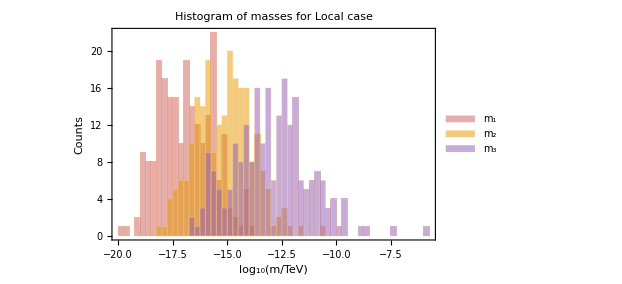
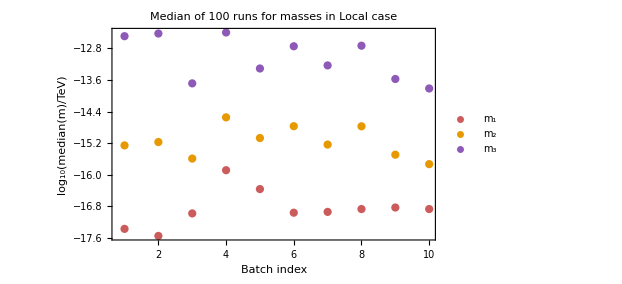

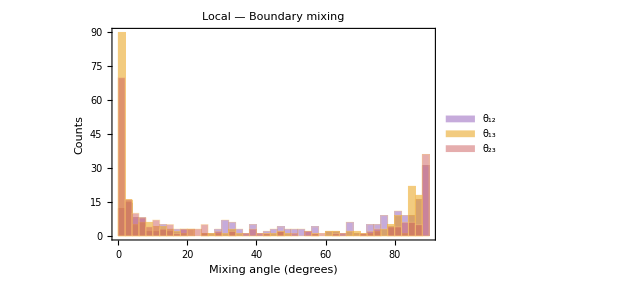

```mathematica
(*STRONG-SITE MAJORANA PARAMETERS.All dimensional inputs are in TeV.*)
majoranaMixing={{1,2/5,3/5},{3/10,1,4/5},{9/10,3/10,1}};

majoranaParameters=Join[TSParameters["StrongSite","Local","Majorana","Boundary"],<|"Sites"->8,"SiteMean"->0,"SiteHalfWidth"->5,"HoppingMean"->1/3,"HoppingHalfWidth"->0,"DecayBase"->5,"DistanceNormalization"->"Numerator","EdgeLaw"->"Uniform",(*No flavour mixing in the tower or endpoint couplings.*)"HamiltonianFlavor"->IdentityMatrix[3],"ActiveCoupling"->173/1000,"ActiveFlavor"->IdentityMatrix[3],"PsiCoupling"->1/5,"PsiFlavor"->IdentityMatrix[3],(*Majorana mass block must be symmetric.Explicitly use (Y+Transpose[Y])/2.*)"MajoranaScale"->5,"MajoranaFlavor"->(majoranaMixing+Transpose[majoranaMixing])/2,"SymmetrizeMajorana"->False,"WorkingPrecision"->80,"MassOrdering"->"Ascending","Seed"->20261009|>];

Dataset[majoranaParameters]
```

```mathematica
(*STRONG-SITE MAJORANA DATA GENERATION Three geometries and two flavour-mixing channels.Uses the numerical inputs in majoranaParameters.*)majoranaAutoSummary=Module[{base=majoranaParameters,mixingMatrix,batchSize=100,batchCount=100,applyRowCut=True,cases,folder,caseFolder,summary={},geometry,channel,p,prefix,seconds,raw,dataFile,summaryFile,row,scanOK,j},If[!StringQ[NotebookDirectory[]],Print["Please save the notebook first."];
Return[$Failed]];
mixingMatrix={{1,2/5,3/5},{3/10,1,4/5},{9/10,3/10,1}};
cases=Tuples[{{"Local","Petersen","NonLocal"},{"Boundary","Hamiltonian"}}];
folder=CreateDirectory[FileNameJoin[{NotebookDirectory[],"MajoranaPlots_"<>DateString[{"Year","Month","Day","_","Hour","Minute","Second"}]}]];
Print["Saving strong-site Majorana data in: ",folder];
Do[{geometry,channel}=cases[[j]];
p=Join[base,<|"Preset"->"StrongSite","Nature"->"Majorana","Geometry"->geometry,"Channel"->channel,"ActiveFlavor"->IdentityMatrix[3],"PsiFlavor"->IdentityMatrix[3],"HamiltonianFlavor"->If[channel==="Hamiltonian",mixingMatrix,IdentityMatrix[3]],"MajoranaFlavor"->If[channel==="Boundary",(mixingMatrix+Transpose[mixingMatrix])/2,IdentityMatrix[3]],"SymmetrizeMajorana"->False|>];
prefix=StringRiffle[{ToLowerCase[geometry],"site_strong",If[channel==="Boundary","majorana_coupling","hamiltonian"],"majorana"},"_"];
caseFolder=CreateDirectory[FileNameJoin[{folder,prefix}]];
Print["[",j,"/",Length[cases],"] Starting ",prefix," | ",batchSize batchCount," trials"];
{seconds,raw}=AbsoluteTiming[TSScan[p,batchSize batchCount,"Parallel"->True]];
(*Save every result before any selection or analysis.ApplyRowCut records the intended downstream selection.*)dataFile=Export[FileNameJoin[{caseFolder,"data.wxf"}],<|"Parameters"->p,"BatchSize"->batchSize,"BatchCount"->batchCount,"ApplyRowCut"->applyRowCut,"Seconds"->seconds,"RawResults"->raw|>,"WXF"];
If[dataFile===$Failed,Print["Data saving failed. Stopping at ",prefix];
Return[<|"Folder"->folder,"CompletedCases"->summary,"UnsavedParameters"->p,"UnsavedRawResults"->raw|>]];
scanOK=ListQ[raw]&&Length[raw]==batchSize batchCount;
row=<|"Case"->prefix,"Parameters"->p,"Seconds"->seconds,"RecordCount"->If[ListQ[raw],Length[raw],0],"Status"->If[scanOK,"Data saved","Incomplete scan saved"],"CaseFolder"->caseFolder,"DataFile"->dataFile|>;
AppendTo[summary,row];
summaryFile=Export[FileNameJoin[{folder,"scan_summary.wxf"}],summary,"WXF"];
If[summaryFile===$Failed,Print["Summary saving failed. Case data are saved."];
Return[<|"Folder"->folder,"Cases"->summary|>]];
Print[row["Status"],": ",prefix," | ",Round[seconds]," seconds"," | records = ",row["RecordCount"]];
Clear[raw];
If[!scanOK,Print["Stopping after the incomplete scan."];
Return[<|"Folder"->folder,"Cases"->summary|>]],{j,Length[cases]}];
<|"Folder"->folder,"Cases"->summary|>];

majoranaAutoSummary
```

### Starting parameters for benchmark search.

```mathematica
(*WEAK SITE DISORDER Paper:Table VII,Eq.(49),Section VI.A and Appendix E.All dimensional inputs are in TeV.*)
ClearAll[WeakSiteParameters];

(*Table VII:geometry-dependent site counts.*)
weakSiteSites=<|"Local"->9,"Petersen"->16,"NonLocal"->16|>;

(*Eq.(49):these two matrices are DIFFERENT.*)
weakSiteYukawa={{1,1/2,2/5},{1/2,1,3/10},{1/2,9/10,1}};

weakSiteHamiltonian={{7/50,1,3/10},{1,1/2,7/20},{2/5,7/10,1}};

(*Edit numerical inputs here.*)
weakSiteNumbers=<|"SiteMean"->10,"SiteHalfWidth"->1/5,(*Uniform[9.8,10.2]*)"HoppingMean"->1/5,"HoppingHalfWidth"->0,"DecayBase"->3,"DistanceNormalization"->"Numerator","EdgeLaw"->"Uniform",(*Endpoint convention retained from our previous scans.*)"ActiveCoupling"->173/1000,"DiracRightCoupling"->173/1000,(*Majorana inputs:Eq.(37),t and W respectively.*)"PsiCoupling"->1/5,"MajoranaScale"->10,"WorkingPrecision"->80,"MassOrdering"->"Ascending","Seed"->20261009|>;

weakSiteBatchSize=100;
weakSiteManualBatchCount=10;    (*1,000 trial samples*)
weakSiteProductionBatchCount=100; (*10,000 per case*)
weakSiteApplyRowCut=True;

(*Construct one case without inheriting StrongSite settings.*)
WeakSiteParameters[geometry_String,nature_String,channel_String]:=Join[TSParameters["WeakSite",geometry,nature,channel],weakSiteNumbers,<|"Sites"->weakSiteSites[geometry],"ActiveFlavor"->IdentityMatrix[3],"PsiFlavor"->IdentityMatrix[3],"HamiltonianFlavor"->If[channel==="Hamiltonian",weakSiteHamiltonian,IdentityMatrix[3]],"DiracRightFlavor"->If[nature==="Dirac"&&channel==="Boundary",weakSiteYukawa,IdentityMatrix[3]],(*Majorana bilinear uses the symmetric part of Eq.(49).*)"MajoranaFlavor"->If[nature==="Majorana"&&channel==="Boundary",(weakSiteYukawa+Transpose[weakSiteYukawa])/2,IdentityMatrix[3]],"SymmetrizeMajorana"->False|>];
```

### Search Algorithm

```mathematica
(*OVERNIGHT WEAK-SITE ANGLE SEARCH Fits a separate flavour matrix for each of 12 cases.Graph parameters remain fixed.All final validation samples are independent of training.*)ClearAll[NFKey,NFWithMatrix,NFShape,NFConstruct,NFValid,NFScore,NFSafeMass,NFInBox,NFSave,NFRunCase];

(*-----Editable controls-----*)

NFSecondsPerCase=20*60;
NFValidationSamples=1000;  (*Must be a positive multiple of 100.*)
NFTrainingSeeds=Range[910001,910012];
NFValidationSeeds=Range[920001,920000+NFValidationSamples];

NFMinEntry=0.05;
NFMaxEntry=3.0;

(*NuFIT 6.1:NO,IC23 without SK atmospheric data.Order everywhere is {theta12,theta13,theta23}.*)
NFTarget={33.76,8.62,43.27};

(*Optimization weights,approximately one-sigma scales.This objective is NOT an experimental chi-squared.*)
NFScale={0.42,0.11,1.0};

NFBounds={{32.54,35.03},{8.27,8.95},{41.11,50.02}};

(*Stop early if the training objective is already very small.*)
NFStopScore=0.1;

(*-----Matrix handling-----*)

NFKey[p_Association]:=Which[p["Channel"]==="Hamiltonian","HamiltonianFlavor",p["Nature"]==="Dirac","DiracRightFlavor",True,"MajoranaFlavor"];

NFWithMatrix[p_Association,m_List]:=Join[p,Association[NFKey[p]->m]];

NFShape[m_List,p_Association]:=Module[{a},a=N[m];
If[p["Nature"]==="Majorana"&&p["Channel"]==="Boundary",a=(a+Transpose[a])/2];
(*Enforce the declared entry-magnitude range.*)a=Map[Function[x,If[x<0,-1,1]*Clip[Abs[x],{NFMinEntry,NFMaxEntry}]],a,{2}];
(*Exact rational entries at six-decimal resolution.*)Round[10^6 a]/10^6];

(*Starting matrices constructed from the target mixing matrix.The subsequent search uses the FULL package calculation.*)
NFConstruct[p_Association]:=Module[{a,b,c,s12,s13,s23,c12,c13,c23,u,m},{a,b,c}=NFTarget Degree;
{s12,s13,s23}=Sin/@{a,b,c};
{c12,c13,c23}=Cos/@{a,b,c};
u={{c12 c13,s12 c13,s13},{-s12 c23-c12 s23 s13,c12 c23-s12 s23 s13,s23 c13},{s12 s23-c12 c23 s13,-c12 s23-s12 c23 s13,c23 c13}};
m=Which[p["Channel"]==="Hamiltonian",DiagonalMatrix[{2,1,1/2}].Transpose[u],p["Nature"]==="Dirac",DiagonalMatrix[{1/2,1,2}].Transpose[u],True,u.DiagonalMatrix[{2,1,1/2}].Transpose[u]];
NFShape[m,p]];

(*-----Sample selection and training objective-----*)

NFValid[r_]:=AssociationQ[r]&&TrueQ[r["NumericallyResolved"]]&&!TrueQ[r["DegenerateLightMasses"]]&&MatchQ[r["AnglesDegrees"],{_?NumericQ,_?NumericQ,_?NumericQ}]&&AllTrue[r["LightMassesTeV"],TrueQ[#>0]&]&&AllTrue[Re[Diagonal[r["PMNS"].ConjugateTranspose[r["PMNS"]]]],TrueQ[99/100<=#<=1+10^-30]&];

(*NFBase and NFBlocks are assigned on each worker per case.*)
NFScore[m_List]:=Module[{p,results,kept,angles,fraction,score},p=NFWithMatrix[NFBase,m];
results=Table[TimeConstrained[TheorySpaceNeutrinos`TSMassFromBlocks[block,p],60,$Failed],{block,NFBlocks}];
kept=Select[results,NFValid];
fraction=N[Length[kept]/Length[results]];
If[kept==={},Return[<|"Matrix"->m,"Score"->10.^9,"AcceptedFraction"->0,"TrainingMedianDegrees"->Missing["NoValidSamples"]|>]];
angles=N[Lookup[kept,"AnglesDegrees"]];
(*Mean squared distance penalizes both displacement and spread.Rejected samples also incur a substantial penalty.*)score=Mean[(Total[((#-NFTarget)/NFScale)^2]&)/@angles]+10000 (1-fraction);
<|"Matrix"->m,"Score"->score,"AcceptedFraction"->fraction,"TrainingMedianDegrees"->(Median/@Transpose[angles])|>];

NFSafeMass[p_Association]:=TimeConstrained[TheorySpaceNeutrinos`TSMass[p],60,Failure["Timeout",<|"MessageTemplate"->"One sample exceeded 60 seconds."|>]];

NFInBox[a_List]:=And@@MapThread[TrueQ[#1<=#2<=#3]&,{NFBounds[[All,1]],a,NFBounds[[All,2]]}];

(*Stop the run explicitly if an essential save fails.*)
NFSave[file_String,value_]:=Module[{out},out=Export[file,value,"WXF"];
If[out===$Failed,Throw[Failure["SaveFailed",<|"MessageTemplate"->"Could not save file.","File"->file|>],"NFDisk"]];
out];

(*-----Search and validation for one case-----*)

NFRunCase[p_Association,root_String,caseNumber_Integer]:=BlockRandom[SeedRandom[73000+caseNumber];
Module[{caseName,caseFolder,blocks,seedMatrix,originalMatrix,populationSize,candidates,scores,elite,best,started,generation=0,history={},sigma,bestParameters,raw,valid,angles,medians,fractionInside,validFraction,precisionCheck,precisionOK,targetMet,fig,plotKeys,plotFiles,row,dataFile,searchSeconds},caseName=StringRiffle[{ToLowerCase[p["Geometry"]],"site_weak",If[p["Channel"]==="Hamiltonian","hamiltonian",If[p["Nature"]==="Dirac","yukawa","majorana_coupling"]],ToLowerCase[p["Nature"]]},"_"];
caseFolder=CreateDirectory[FileNameJoin[{root,caseName}]];
Print["Starting ",caseName," | Sites = ",p["Sites"]];
(*Identical disorder samples for every candidate in this case.*)blocks=Table[TheorySpaceNeutrinos`TSGenerateBlocks[Join[p,<|"Seed"->s|>]],{s,NFTrainingSeeds}];
If[!AllTrue[blocks,ListQ],NFSave[FileNameJoin[{caseFolder,"generation_failure.wxf"}],<|"Parameters"->p,"Blocks"->blocks|>];
Return[<|"Case"->caseName,"Status"->"Random-block generation failed","CaseFolder"->caseFolder|>]];
(*Cache blocks on workers instead of repeatedly transmitting them.*)With[{pp=p,bb=blocks},ParallelEvaluate[NFBase=pp;
NFBlocks=bb;
Null]];
populationSize=Max[16,2 Length[Kernels[]]];
seedMatrix=NFConstruct[p];
originalMatrix=NFShape[p[NFKey[p]],p];
candidates=Join[{originalMatrix,seedMatrix},Table[NFShape[seedMatrix+0.1 RandomVariate[NormalDistribution[],{3,3}],p],{populationSize-2}]];
started=SessionTime[];
scores=ParallelMap[NFScore,candidates,DistributedContexts->None];
elite=Take[SortBy[scores,#["Score"]&],UpTo[4]];
best=First[elite];
(*Search with elitism,several step sizes,and random restarts.*)While[SessionTime[]-started<NFSecondsPerCase&&best["Score"]>NFStopScore,generation++;
candidates=Table[If[RandomReal[]<0.15,NFShape[RandomReal[{-2,2},{3,3}],p],sigma=RandomChoice[{0.001,0.003,0.01,0.03,0.1,0.3}];
NFShape[RandomChoice[Lookup[elite,"Matrix"]]+sigma RandomVariate[NormalDistribution[],{3,3}],p]],{populationSize}];
scores=ParallelMap[NFScore,candidates,DistributedContexts->None];
elite=Take[SortBy[Join[elite,scores],#["Score"]&],UpTo[4]];
best=First[elite];
AppendTo[history,{generation,SessionTime[]-started,best["Score"]}];
NFSave[FileNameJoin[{caseFolder,"best_so_far.wxf"}],<|"BaseParameters"->p,"Best"->best,"TrainingSeeds"->NFTrainingSeeds,"TargetAnglesDegrees"->NFTarget,"ObjectiveScalesDegrees"->NFScale,"History"->history|>];
If[Mod[generation,10]==0,Print[caseName," | generation ",generation," | score ",best["Score"]," | training medians ",best["TrainingMedianDegrees"]]];];
searchSeconds=SessionTime[]-started;
bestParameters=Join[NFWithMatrix[p,best["Matrix"]],<|"Seed"->First[NFValidationSeeds]|>];
(*Save the exact candidate before any validation work.*)NFSave[FileNameJoin[{caseFolder,"best_so_far.wxf"}],<|"Parameters"->bestParameters,"Best"->best,"TrainingSeeds"->NFTrainingSeeds,"TargetAnglesDegrees"->NFTarget,"ObjectiveScalesDegrees"->NFScale,"SearchSeconds"->searchSeconds,"History"->history|>];
Print["Validating ",caseName," on ",NFValidationSamples," fresh samples."];
(*Validation data are never used to tune this candidate.*)With[{pp=bestParameters},raw=ParallelMap[NFSafeMass[Join[pp,<|"Seed"->#|>]]&,NFValidationSeeds,DistributedContexts->None]];
dataFile=NFSave[FileNameJoin[{caseFolder,"data.wxf"}],<|"Parameters"->bestParameters,"BatchSize"->100,"BatchCount"->NFValidationSamples/100,"ApplyRowCut"->True,"TrainingSeeds"->NFTrainingSeeds,"ValidationSeeds"->NFValidationSeeds,"TargetAnglesDegrees"->NFTarget,"AngleBoundsDegrees"->NFBounds,"RawResults"->raw|>];
valid=Select[raw,NFValid];
validFraction=N[Length[valid]/Length[raw]];
angles=If[valid==={},{},N[Lookup[valid,"AnglesDegrees"]]];
medians=If[angles==={},Missing["NoValidSamples"],Median/@Transpose[angles]];
(*Denominator includes ALL attempted validation samples.Failed or rejected samples do not disappear from this fraction.*)fractionInside=N[Count[NFInBox/@angles,True]/Length[raw]];
precisionCheck=TheorySpaceNeutrinos`TSPrecisionCheck[bestParameters,20];
NFSave[FileNameJoin[{caseFolder,"precision_check.wxf"}],precisionCheck];
precisionOK=AssociationQ[precisionCheck]&&TrueQ[Lookup[precisionCheck,"Pass",False]];
(*Operational success criterion:
>=90% of all trials inside all three marginal 3-sigma ranges,medians within the chosen objective scales,precision check passes.This is NOT a joint experimental confidence region.*)targetMet=angles=!={}&&fractionInside>=0.90&&Max[Abs[(medians-NFTarget)/NFScale]]<=1&&precisionOK;
row=<|"Case"->caseName,"Status"->If[targetMet,"Angle target met","Needs more work"],"MatrixKey"->NFKey[p],"BestMatrix"->best["Matrix"],"Parameters"->bestParameters,"TrainingScore"->best["Score"],"ValidationMedianDegrees"->medians,"ValidAngleFraction"->validFraction,"FractionAllTrialsInside3Sigma"->fractionInside,"PrecisionCheckPassed"->precisionOK,"SearchSeconds"->searchSeconds,"CaseFolder"->caseFolder,"DataFile"->dataFile|>;
NFSave[FileNameJoin[{caseFolder,"benchmark.wxf"}],row];
Print[caseName," | ",row["Status"]," | validation medians = ",medians," | fraction inside ranges = ",fractionInside];
row]];
```

```mathematica
overnightFitSummary=Catch[Module[{packagePath,loaded,cases,root,summary={},geometry,nature,channel,p,row,j},If[!StringQ[NotebookDirectory[]],Print["Save the notebook before starting."];
Return[$Failed]];
If[!IntegerQ[NFValidationSamples]||NFValidationSamples<=0||Mod[NFValidationSamples,100]!=0,Print["NFValidationSamples must be a positive multiple of 100."];
Return[$Failed]];
If[!And@@(Length[DownValues[#]]>0&/@{WeakSiteParameters,NFRunCase,NFSave}),Print["First evaluate the starting-parameter and angle-search definitions."];
Return[$Failed]];
packagePath=FileNameJoin[{NotebookDirectory[],"TheorySpaceNeutrinos.wl"}];
If[!FileExistsQ[packagePath],Print["Package not found: ",packagePath];
Return[$Failed]];
If[Length[Kernels[]]==0,LaunchKernels[]];
With[{path=packagePath},loaded=ParallelEvaluate[Get[path];
Length[DownValues[TheorySpaceNeutrinos`TSMass]]>0]];
If[loaded==={}||!AllTrue[loaded,TrueQ],Print["Package loading failed on one or more workers."];
Return[$Failed]];
DistributeDefinitions[NFKey,NFWithMatrix,NFValid,NFScore,NFSafeMass,NFTarget,NFScale];
cases=Tuples[{{"Local","Petersen","NonLocal"},{"Dirac","Majorana"},{"Boundary","Hamiltonian"}}];
root=CreateDirectory[FileNameJoin[{NotebookDirectory[],"WeakSite_AngleSearch_"<>DateString[{"Year","Month","Day","_","Hour","Minute","Second"}]}]];
NFSave[FileNameJoin[{root,"search_settings.wxf"}],<|"TargetAnglesDegrees"->NFTarget,"ObjectiveScalesDegrees"->NFScale,"AngleBoundsDegrees"->NFBounds,"TrainingSeeds"->NFTrainingSeeds,"ValidationSeeds"->NFValidationSeeds,"SecondsPerCase"->NFSecondsPerCase,"AllowedEntryMagnitudes"->{NFMinEntry,NFMaxEntry},"FitSource"->"NuFIT 6.1 NO, IC23 without SK atmospheric data","MassesAndCPPhaseFitted"->False|>];
Print["Output folder: ",root];
Print["Cases: ",Length[cases]," | Workers: ",Length[Kernels[]]];
Do[{geometry,nature,channel}=cases[[j]];
p=WeakSiteParameters[geometry,nature,channel];
Print["Case ",j,"/",Length[cases]];
row=NFRunCase[p,root,j];
AppendTo[summary,row];
NFSave[FileNameJoin[{root,"summary.wxf"}],<|"Folder"->root,"Cases"->summary|>];,{j,Length[cases]}];
<|"Folder"->root,"Cases"->summary|>],"NFDisk"];

If[AssociationQ[overnightFitSummary],Dataset[KeyTake[#,{"Case","Status","ValidationMedianDegrees","FractionAllTrialsInside3Sigma","PrecisionCheckPassed"}]&/@overnightFitSummary["Cases"]],overnightFitSummary]
```

Output folder: /home/as/Documents/Wolfram_Mathematica/Codes/Anderson/Submission_Randomness/Unified_Neutrino_Model/WeakSite_AngleSearch_20261010_192103

Cases: 12 | Workers: 8

Case 1/12

Starting local_site_weak_yukawa_dirac | Sites = 9

local_site_weak_yukawa_dirac | generation 10 | score 38.8859 | training medians {33.1291,8.56931,42.8853}

local_site_weak_yukawa_dirac | generation 20 | score 36.6803 | training medians {32.9046,8.59879,42.2276}

local_site_weak_yukawa_dirac | generation 30 | score 33.6436 | training medians {33.2639,8.5903,42.8171}

local_site_weak_yukawa_dirac | generation 40 | score 32.9358 | training medians {33.3341,8.63046,42.9334}

local_site_weak_yukawa_dirac | generation 50 | score 32.5241 | training medians {33.2528,8.64294,42.8261}

local_site_weak_yukawa_dirac | generation 60 | score 30.2422 | training medians {33.5101,8.6265,43.0433}

local_site_weak_yukawa_dirac | generation 70 | score 29.91 | training medians {33.3812,8.57999,43.0504}

local_site_weak_yukawa_dirac | generation 80 | score 29.6799 | training medians {33.3733,8.62967,43.1384}

local_site_weak_yukawa_dirac | generation 90 | score 29.3579 | training medians {33.4191,8.6121,43.2973}

local_site_weak_yukawa_dirac | generation 100 | score 29.291 | training medians {33.3522,8.59415,43.412}

local_site_weak_yukawa_dirac | generation 110 | score 29.1478 | training medians {33.3628,8.61999,43.4331}

local_site_weak_yukawa_dirac | generation 120 | score 28.3544 | training medians {33.2918,8.60138,43.5911}

local_site_weak_yukawa_dirac | generation 130 | score 28.2363 | training medians {33.3507,8.58952,43.5108}

local_site_weak_yukawa_dirac | generation 140 | score 28.1259 | training medians {33.3947,8.59296,43.5082}

local_site_weak_yukawa_dirac | generation 150 | score 28.0911 | training medians {33.3946,8.62033,43.5447}

local_site_weak_yukawa_dirac | generation 160 | score 27.7305 | training medians {33.351,8.61429,43.6696}

local_site_weak_yukawa_dirac | generation 170 | score 27.5551 | training medians {33.3548,8.58397,43.5217}

local_site_weak_yukawa_dirac | generation 180 | score 27.0394 | training medians {33.3542,8.56612,43.0294}

local_site_weak_yukawa_dirac | generation 190 | score 26.9386 | training medians {33.4169,8.60393,43.0886}

local_site_weak_yukawa_dirac | generation 200 | score 26.9077 | training medians {33.3637,8.58783,43.0401}

local_site_weak_yukawa_dirac | generation 210 | score 26.5603 | training medians {33.3326,8.56197,43.2269}

local_site_weak_yukawa_dirac | generation 220 | score 26.3756 | training medians {33.5043,8.59419,43.35}

local_site_weak_yukawa_dirac | generation 230 | score 26.2941 | training medians {33.2728,8.59267,43.332}

local_site_weak_yukawa_dirac | generation 240 | score 26.2494 | training medians {33.3463,8.56541,43.3025}

local_site_weak_yukawa_dirac | generation 250 | score 26.1944 | training medians {33.3871,8.60248,43.3343}

local_site_weak_yukawa_dirac | generation 260 | score 26.0564 | training medians {33.4326,8.58167,43.2964}

local_site_weak_yukawa_dirac | generation 270 | score 25.9508 | training medians {33.3181,8.61524,43.3695}

local_site_weak_yukawa_dirac | generation 280 | score 25.7992 | training medians {33.448,8.58421,43.3177}

local_site_weak_yukawa_dirac | generation 290 | score 25.7548 | training medians {33.3122,8.57713,43.4276}

local_site_weak_yukawa_dirac | generation 300 | score 25.6236 | training medians {33.4182,8.58278,43.4389}

local_site_weak_yukawa_dirac | generation 310 | score 25.6196 | training medians {33.4359,8.59601,43.4322}

local_site_weak_yukawa_dirac | generation 320 | score 25.5588 | training medians {33.3714,8.57598,43.4807}

Validating local_site_weak_yukawa_dirac on 1000 fresh samples.

local_site_weak_yukawa_dirac | Needs more work | validation medians = {33.6181,8.54298,43.3306} | fraction inside ranges = 0.496

Case 2/12

Starting local_site_weak_hamiltonian_dirac | Sites = 9

local_site_weak_hamiltonian_dirac | generation 10 | score 55.7366 | training medians {33.9933,8.77062,42.8902}

local_site_weak_hamiltonian_dirac | generation 20 | score 54.908 | training medians {33.9012,8.77014,42.8148}

local_site_weak_hamiltonian_dirac | generation 30 | score 54.5804 | training medians {33.787,8.82811,43.0382}

local_site_weak_hamiltonian_dirac | generation 40 | score 53.6459 | training medians {33.7895,8.75431,43.0665}

local_site_weak_hamiltonian_dirac | generation 50 | score 52.6959 | training medians {34.0251,8.7586,42.9352}

local_site_weak_hamiltonian_dirac | generation 60 | score 48.9886 | training medians {34.1861,8.85437,41.8335}

local_site_weak_hamiltonian_dirac | generation 70 | score 47.2998 | training medians {33.9306,8.79252,42.1432}

local_site_weak_hamiltonian_dirac | generation 80 | score 45.8215 | training medians {33.7381,8.95472,42.813}

local_site_weak_hamiltonian_dirac | generation 90 | score 40.3165 | training medians {33.9282,8.77068,42.7584}

local_site_weak_hamiltonian_dirac | generation 100 | score 36.0612 | training medians {34.3378,8.75045,42.466}

local_site_weak_hamiltonian_dirac | generation 110 | score 33.352 | training medians {33.9446,8.73531,43.0765}

local_site_weak_hamiltonian_dirac | generation 120 | score 32.9212 | training medians {34.0426,8.74126,42.7516}

local_site_weak_hamiltonian_dirac | generation 130 | score 32.8317 | training medians {34.0166,8.77637,42.8346}

local_site_weak_hamiltonian_dirac | generation 140 | score 32.5136 | training medians {33.8559,8.77387,42.8357}

local_site_weak_hamiltonian_dirac | generation 150 | score 32.2722 | training medians {34.0861,8.7598,42.8295}

local_site_weak_hamiltonian_dirac | generation 160 | score 31.4475 | training medians {34.0399,8.74493,43.4577}

local_site_weak_hamiltonian_dirac | generation 170 | score 30.6243 | training medians {34.1219,8.69722,42.96}

local_site_weak_hamiltonian_dirac | generation 180 | score 30.1781 | training medians {33.9762,8.75351,42.8751}

local_site_weak_hamiltonian_dirac | generation 190 | score 29.8058 | training medians {34.0869,8.72465,42.8392}

local_site_weak_hamiltonian_dirac | generation 200 | score 29.6799 | training medians {34.0939,8.74697,42.9241}

local_site_weak_hamiltonian_dirac | generation 210 | score 28.9014 | training medians {34.0345,8.73422,43.1164}

local_site_weak_hamiltonian_dirac | generation 220 | score 28.8933 | training medians {34.1332,8.70677,43.1122}

local_site_weak_hamiltonian_dirac | generation 230 | score 28.659 | training medians {34.0649,8.7466,43.2708}

local_site_weak_hamiltonian_dirac | generation 240 | score 28.5594 | training medians {34.1343,8.76167,43.3241}

Validating local_site_weak_hamiltonian_dirac on 1000 fresh samples.

local_site_weak_hamiltonian_dirac | Needs more work | validation medians = {33.6412,8.62966,42.7032} | fraction inside ranges = 0.242

Case 3/12

Starting local_site_weak_majorana_coupling_majorana | Sites = 9

local_site_weak_majorana_coupling_majorana | generation 10 | score 86.6006 | training medians {33.102,8.66131,46.8566}

local_site_weak_majorana_coupling_majorana | generation 20 | score 78.0053 | training medians {32.9607,8.56847,46.0861}

local_site_weak_majorana_coupling_majorana | generation 30 | score 68.4617 | training medians {33.51,8.63292,44.6238}

local_site_weak_majorana_coupling_majorana | generation 40 | score 67.0705 | training medians {33.4017,8.57814,44.4715}

Validating local_site_weak_majorana_coupling_majorana on 1000 fresh samples.

local_site_weak_majorana_coupling_majorana | Needs more work | validation medians = {33.9022,8.46249,44.3536} | fraction inside ranges = 0.263

Case 4/12

Starting local_site_weak_hamiltonian_majorana | Sites = 9

local_site_weak_hamiltonian_majorana | generation 10 | score 58.4744 | training medians {33.8889,8.76815,43.0909}

local_site_weak_hamiltonian_majorana | generation 20 | score 56.9988 | training medians {33.5714,8.74706,43.179}

local_site_weak_hamiltonian_majorana | generation 30 | score 56.2336 | training medians {33.6934,8.81557,42.9467}

local_site_weak_hamiltonian_majorana | generation 40 | score 55.8381 | training medians {33.6332,8.80065,43.1371}

local_site_weak_hamiltonian_majorana | generation 50 | score 52.9959 | training medians {33.8233,8.83893,42.7912}

Validating local_site_weak_hamiltonian_majorana on 1000 fresh samples.

local_site_weak_hamiltonian_majorana | Needs more work | validation medians = {33.474,8.65805,42.7115} | fraction inside ranges = 0.151

Case 5/12

Starting petersen_site_weak_yukawa_dirac | Sites = 16

petersen_site_weak_yukawa_dirac | generation 10 | score 16.8639 | training medians {33.8325,8.72099,44.1803}

petersen_site_weak_yukawa_dirac | generation 20 | score 15.8426 | training medians {33.7486,8.658,43.8911}

petersen_site_weak_yukawa_dirac | generation 30 | score 15.5649 | training medians {33.776,8.67547,43.8653}

petersen_site_weak_yukawa_dirac | generation 40 | score 15.4895 | training medians {33.7567,8.66378,43.7708}

petersen_site_weak_yukawa_dirac | generation 50 | score 15.4813 | training medians {33.7288,8.69484,43.7795}

petersen_site_weak_yukawa_dirac | generation 60 | score 15.3527 | training medians {33.7773,8.68019,43.7403}

petersen_site_weak_yukawa_dirac | generation 70 | score 15.3332 | training medians {33.7491,8.66037,43.7808}

Validating petersen_site_weak_yukawa_dirac on 1000 fresh samples.

petersen_site_weak_yukawa_dirac | Needs more work | validation medians = {33.6106,8.52848,43.0677} | fraction inside ranges = 0.537

Case 6/12

Starting petersen_site_weak_hamiltonian_dirac | Sites = 16

petersen_site_weak_hamiltonian_dirac | generation 10 | score 40.0145 | training medians {33.6461,8.68452,43.5032}

petersen_site_weak_hamiltonian_dirac | generation 20 | score 37.9635 | training medians {33.4414,8.63141,43.4852}

petersen_site_weak_hamiltonian_dirac | generation 30 | score 37.4619 | training medians {33.4342,8.63206,43.1851}

petersen_site_weak_hamiltonian_dirac | generation 40 | score 36.4169 | training medians {33.4339,8.5814,42.253}

petersen_site_weak_hamiltonian_dirac | generation 50 | score 35.9361 | training medians {33.6279,8.66172,42.4887}

Validating petersen_site_weak_hamiltonian_dirac on 1000 fresh samples.

petersen_site_weak_hamiltonian_dirac | Needs more work | validation medians = {33.6596,8.64199,42.1042} | fraction inside ranges = 0.365

Case 7/12

Starting petersen_site_weak_majorana_coupling_majorana | Sites = 16

petersen_site_weak_majorana_coupling_majorana | generation 10 | score 49.4217 | training medians {33.6545,8.65377,44.1341}

Validating petersen_site_weak_majorana_coupling_majorana on 1000 fresh samples.

petersen_site_weak_majorana_coupling_majorana | Needs more work | validation medians = {33.1033,8.49128,43.236} | fraction inside ranges = 0.218

Case 8/12

Starting petersen_site_weak_hamiltonian_majorana | Sites = 16

petersen_site_weak_hamiltonian_majorana | generation 10 | score 41.951 | training medians {33.5816,8.62691,43.5692}

Validating petersen_site_weak_hamiltonian_majorana on 1000 fresh samples.

petersen_site_weak_hamiltonian_majorana | Needs more work | validation medians = {33.6402,8.60718,43.2638} | fraction inside ranges = 0.376

Case 9/12

Starting nonlocal_site_weak_yukawa_dirac | Sites = 16

nonlocal_site_weak_yukawa_dirac | generation 10 | score 13.369 | training medians {33.875,8.53512,43.5908}

nonlocal_site_weak_yukawa_dirac | generation 20 | score 13.2813 | training medians {33.8104,8.54402,43.3783}

nonlocal_site_weak_yukawa_dirac | generation 30 | score 13.2217 | training medians {33.7966,8.55225,43.4162}

nonlocal_site_weak_yukawa_dirac | generation 40 | score 13.2217 | training medians {33.7966,8.55225,43.4162}

nonlocal_site_weak_yukawa_dirac | generation 50 | score 13.2035 | training medians {33.6089,8.51201,43.4082}

nonlocal_site_weak_yukawa_dirac | generation 60 | score 12.5102 | training medians {33.7111,8.58633,43.6967}

nonlocal_site_weak_yukawa_dirac | generation 70 | score 12.3908 | training medians {33.84,8.56197,43.5965}

Validating nonlocal_site_weak_yukawa_dirac on 1000 fresh samples.

nonlocal_site_weak_yukawa_dirac | Needs more work | validation medians = {33.5729,8.5677,43.4038} | fraction inside ranges = 0.672

Case 10/12

Starting nonlocal_site_weak_hamiltonian_dirac | Sites = 16

nonlocal_site_weak_hamiltonian_dirac | generation 10 | score 21.7587 | training medians {33.7231,8.63761,43.4105}

nonlocal_site_weak_hamiltonian_dirac | generation 20 | score 21.4757 | training medians {33.6594,8.61562,43.2086}

nonlocal_site_weak_hamiltonian_dirac | generation 30 | score 21.2229 | training medians {33.4987,8.5749,43.6928}

nonlocal_site_weak_hamiltonian_dirac | generation 40 | score 20.6773 | training medians {33.699,8.60099,43.4763}

nonlocal_site_weak_hamiltonian_dirac | generation 50 | score 20.581 | training medians {33.5969,8.60738,43.4182}

Validating nonlocal_site_weak_hamiltonian_dirac on 1000 fresh samples.

nonlocal_site_weak_hamiltonian_dirac | Needs more work | validation medians = {33.6197,8.87778,43.2813} | fraction inside ranges = 0.431

Case 11/12

Starting nonlocal_site_weak_majorana_coupling_majorana | Sites = 16

nonlocal_site_weak_majorana_coupling_majorana | generation 10 | score 24.9092 | training medians {34.2128,8.56289,43.7733}

Validating nonlocal_site_weak_majorana_coupling_majorana on 1000 fresh samples.

nonlocal_site_weak_majorana_coupling_majorana | Needs more work | validation medians = {33.6944,8.57782,43.516} | fraction inside ranges = 0.445

Case 12/12

Starting nonlocal_site_weak_hamiltonian_majorana | Sites = 16

nonlocal_site_weak_hamiltonian_majorana | generation 10 | score 21.5235 | training medians {33.4933,8.63792,43.0363}

Validating nonlocal_site_weak_hamiltonian_majorana on 1000 fresh samples.

nonlocal_site_weak_hamiltonian_majorana | Needs more work | validation medians = {33.5242,8.89115,43.031} | fraction inside ranges = 0.414

```mathematica
(*Optional inspection of masses from the angle-search results.Requires overnightFitSummary and the search helper definitions.Not needed when generating data from frozen benchmarks.*)
massOverview=Table[Module[{saved,raw,kept,masses,splittings},saved=Import[entry["DataFile"],"WXF"];
If[!AssociationQ[saved],Return[<|"Case"->entry["Case"],"Status"->"Could not load data"|>]];
raw=Lookup[saved,"RawResults",{}];
kept=If[ListQ[raw],Select[raw,NFValid],{}];
If[kept==={},Return[<|"Case"->entry["Case"],"Status"->"No valid samples"|>]];
(*Convert TeV to eV before computing splittings.*)masses=10^12 Lookup[kept,"LightMassesTeV"];
splittings=({#[[2]]^2-#[[1]]^2,#[[3]]^2-#[[1]]^2}&)/@masses;
<|"Case"->entry["Case"],"Median masses (eV)"->N[Median/@Transpose[masses],5],"Median sum (eV)"->N[Median[Total/@masses],5],"Median {Delta21, Delta31} (eV^2)"->N[Median/@Transpose[splittings],5],"Median Delta21/Delta31"->N[Median[(#[[1]]/#[[2]]&)/@splittings],5]|>],{entry,overnightFitSummary["Cases"]}];

Dataset[massOverview]
```

```mathematica
(*MASS-TUNING SEARCH Requires the angle-search helper definitions and overnightFitSummary.Flavour matrices remain fixed.SiteMean=10 and SiteHalfWidth=1/5 remain unchanged.Majorana PsiCoupling follows the graph hopping t.*)
ClearAll[MTParameters,MTMeasure,MTEvaluate,MTRunCase];

MTTrainingSeeds=Range[930001,930005];
MTValidationSeeds=Range[940001,941000];

(*Same normal-ordering fit used for the angle search.*)
MTTargetSplittings={7.537*10^-5,2.521*10^-3};

(*Broad angle weights for this qualitative mass search.*)
MTAngleScales={1.5,0.35,3.0};

(*Coarse search ranges;all dimensional entries are in TeV.*)
MTSites=<|"Local"->{4,5,6,7,8,9},"Petersen"->{8,12,16,20},"NonLocal"->{8,12,16,20}|>;

MTHoppings={1/20,1/10,1/5,2/5,7/10,1,3/2,2,3};
MTDecayBases={3/2,2,3,4,5};


(*Construct a trial without modifying its flavour matrices.*)
MTParameters[base_Association,sites_,hopping_,decay_]:=Join[base,<|"Sites"->sites,"HoppingMean"->hopping,"HoppingHalfWidth"->0,"DecayBase"->decay|>,If[base["Nature"]==="Majorana",<|"PsiCoupling"->hopping|>,<||>]];


(*Summarize one ensemble and assign its search score.*)
MTMeasure[raw_List]:=Module[{kept,masses,angles,splittings,medianMasses,medianAngles,medianSplittings,fraction,score},kept=Select[raw,NFValid];
fraction=N[Length[kept]/Length[raw]];
If[kept==={},Return[<|"Score"->10.^12,"ValidFraction"->0,"Status"->"No valid samples"|>]];
masses=10^12 Lookup[kept,"LightMassesTeV"];
angles=N[Lookup[kept,"AnglesDegrees"]];
splittings=({#[[2]]^2-#[[1]]^2,#[[3]]^2-#[[1]]^2}&)/@masses;
medianMasses=N[Median/@Transpose[masses]];
medianAngles=Median/@Transpose[angles];
medianSplittings=N[Median/@Transpose[splittings]];
If[!AllTrue[medianSplittings,TrueQ[#>0]&],Return[<|"Score"->10.^12,"ValidFraction"->fraction,"Status"->"Invalid splittings"|>]];
(*Logarithmic mass penalty handles many orders of magnitude.Angle penalty includes both displacement and spread.Rejected samples are penalized rather than silently discarded.*)score=Total[(Log[10,medianSplittings/MTTargetSplittings]/0.5)^2]+Mean[(Total[((#-NFTarget)/MTAngleScales)^2]&)/@angles]+100 (1-fraction);
<|"Score"->score,"ValidFraction"->fraction,"MedianMassesEV"->medianMasses,"MedianMassSumEV"->N[Median[Total/@masses]],"MedianAnglesDegrees"->medianAngles,"MedianSplittingsEV2"->medianSplittings,"MedianSplittingRatio"->N[Median[(#[[1]]/#[[2]]&)/@splittings]],"AngleRangeFractionAllTrials"->N[Count[NFInBox/@angles,True]/Length[raw]]|>];


MTEvaluate[p_Association]:=Module[{raw},raw=Table[NFSafeMass[Join[p,<|"Seed"->seed|>]],{seed,MTTrainingSeeds}];
Join[<|"Parameters"->p|>,MTMeasure[raw]]];


MTRunCase[entry_Association,root_String]:=Module[{base,geometry,caseName,folder,decays,trials,scored,pool,best,refined,leaders,factors,newHopping,p,raw,validation,precision,precisionOK,ballpark,fig,plotKeys,plotFiles,result,width},base=entry["Parameters"];
geometry=base["Geometry"];
caseName=entry["Case"];
folder=CreateDirectory[FileNameJoin[{root,caseName}]];
decays=If[geometry==="Local",{base["DecayBase"]},MTDecayBases];
Print["Coarse mass search: ",caseName];
trials=Prepend[Flatten[Table[MTParameters[base,n,t,b],{n,MTSites[geometry]},{t,MTHoppings},{b,decays}],2],base];
trials=DeleteDuplicates[trials];
scored=ParallelMap[MTEvaluate,trials,DistributedContexts->None];
NFSave[FileNameJoin[{folder,"coarse_search.wxf"}],scored];
pool=SortBy[Select[scored,#["Score"]<10.^11&],#["Score"]&];
If[pool==={},result=<|"Case"->caseName,"Status"->"No valid coarse candidate","CaseFolder"->folder|>;
NFSave[FileNameJoin[{folder,"benchmark.wxf"}],result];
Return[result]];
(*Refine hopping around the best few discrete choices.First broad refinement,then finer refinement.Site count and decay base stay fixed within each refinement.*)Do[leaders=Take[pool,UpTo[3]];
factors=10.^Subdivide[-width,width,12];
refined=Flatten[Table[p=leader["Parameters"];
newHopping=Round[10^6 p["HoppingMean"] factor]/10^6;
MTParameters[p,p["Sites"],Clip[newHopping,{1/1000,4}],p["DecayBase"]],{leader,leaders},{factor,factors}],1];
scored=ParallelMap[MTEvaluate,DeleteDuplicates[refined],DistributedContexts->None];
pool=Take[SortBy[Join[pool,Select[scored,#["Score"]<10.^11&]],#["Score"]&],UpTo[20]];
NFSave[FileNameJoin[{folder,"best_so_far.wxf"}],pool];
Print[caseName," | best training masses (eV): ",First[pool]["MedianMassesEV"]," | angles: ",First[pool]["MedianAnglesDegrees"]];,{width,{0.25,0.05}}];
best=First[pool];
p=Join[best["Parameters"],<|"Seed"->First[MTValidationSeeds]|>];
Print["Fresh validation: ",caseName];
With[{pp=p},raw=ParallelMap[NFSafeMass[Join[pp,<|"Seed"->#|>]]&,MTValidationSeeds,DistributedContexts->None]];
(*Save expensive validation records before plotting.*)NFSave[FileNameJoin[{folder,"data.wxf"}],<|"Parameters"->p,"BatchSize"->100,"BatchCount"->Length[MTValidationSeeds]/100,"ApplyRowCut"->True,"TrainingSeeds"->MTTrainingSeeds,"ValidationSeeds"->MTValidationSeeds,"RawResults"->raw|>];
validation=MTMeasure[raw];
precision=TheorySpaceNeutrinos`TSPrecisionCheck[p,20];
NFSave[FileNameJoin[{folder,"precision_check.wxf"}],precision];
precisionOK=AssociationQ[precision]&&TrueQ[Lookup[precision,"Pass",False]];
(*Qualitative benchmark criterion:median splittings within a factor of 3 of targets;
median angles inside the chosen marginal ranges;
at least 90% valid samples;precision check passes.This is not an experimental acceptance test.*)ballpark=KeyExistsQ[validation,"MedianSplittingsEV2"]&&validation["ValidFraction"]>=0.90&&NFInBox[validation["MedianAnglesDegrees"]]&&AllTrue[validation["MedianSplittingsEV2"]/MTTargetSplittings,TrueQ[1/3<=#<=3]&]&&precisionOK;
result=Join[validation,<|"Case"->caseName,"Status"->If[ballpark,"Ballpark benchmark found","Best candidate; inspect results"],"Parameters"->p,"Sites"->p["Sites"],"HoppingMean"->p["HoppingMean"],"DecayBase"->p["DecayBase"],"PrecisionCheckPassed"->precisionOK,"CaseFolder"->folder|>];
NFSave[FileNameJoin[{folder,"benchmark.wxf"}],result];
Print[caseName," | ",result["Status"]," | masses (eV): ",Lookup[result,"MedianMassesEV",Missing["Unavailable"]]," | angles: ",Lookup[result,"MedianAnglesDegrees",Missing["Unavailable"]]];
result];


(*-----Run all 12 cases-----*)

massTuningSummary=Catch[Module[{root,packagePath,loaded,summary={},row},If[!StringQ[NotebookDirectory[]],Print["Save the notebook first."];
Return[$Failed]];
If[!AssociationQ[overnightFitSummary],Print["Load overnightFitSummary first."];
Return[$Failed]];
packagePath=FileNameJoin[{NotebookDirectory[],"TheorySpaceNeutrinos.wl"}];
If[!FileExistsQ[packagePath],Print["Package not found: ",packagePath];
Return[$Failed]];
If[Length[Kernels[]]==0,LaunchKernels[]];
With[{path=packagePath},loaded=ParallelEvaluate[Get[path];
Length[DownValues[TheorySpaceNeutrinos`TSMass]]>0]];
If[loaded==={}||!AllTrue[loaded,TrueQ],Print["Package loading failed on a worker."];
Return[$Failed]];
DistributeDefinitions[NFValid,NFSafeMass,NFInBox,NFTarget,NFBounds,MTMeasure,MTEvaluate,MTTrainingSeeds,MTTargetSplittings,MTAngleScales];
root=CreateDirectory[FileNameJoin[{NotebookDirectory[],"WeakSite_MassTuning_"<>DateString[{"Year","Month","Day","_","Hour","Minute","Second"}]}]];
NFSave[FileNameJoin[{root,"search_settings.wxf"}],<|"Sites"->MTSites,"HoppingsTeV"->MTHoppings,"DecayBases"->MTDecayBases,"TrainingSeeds"->MTTrainingSeeds,"ValidationSeeds"->MTValidationSeeds,"TargetSplittingsEV2"->MTTargetSplittings,"TargetAnglesDegrees"->NFTarget,"MajoranaPsiCouplingFollowsHopping"->True,"FlavourMatricesFixed"->True|>];
Print["Saving in: ",root];
Do[row=MTRunCase[entry,root];
AppendTo[summary,row];
NFSave[FileNameJoin[{root,"summary.wxf"}],<|"Folder"->root,"Cases"->summary|>];,{entry,overnightFitSummary["Cases"]}];
<|"Folder"->root,"Cases"->summary|>],"NFDisk"];

If[AssociationQ[massTuningSummary],Dataset[KeyTake[#,{"Case","Status","Sites","HoppingMean","DecayBase","MedianMassesEV","MedianMassSumEV","MedianSplittingsEV2","MedianAnglesDegrees","PrecisionCheckPassed"}]&/@massTuningSummary["Cases"]],massTuningSummary]
```

Saving in: /home/as/Documents/Wolfram_Mathematica/Codes/Anderson/Submission_Randomness/Unified_Neutrino_Model/WeakSite_MassTuning_20261011_092129

Coarse mass search: local_site_weak_yukawa_dirac

local_site_weak_yukawa_dirac | best training masses (eV): {0.00308102,0.01302,0.0435799} | angles: {33.2661,8.66466,44.5742}

local_site_weak_yukawa_dirac | best training masses (eV): {0.00282033,0.0119593,0.0395304} | angles: {34.4043,8.62751,42.3441}

Fresh validation: local_site_weak_yukawa_dirac

local_site_weak_yukawa_dirac | Ballpark benchmark found | masses (eV): {0.00278045,0.0118048,0.0392373} | angles: {33.6466,8.55179,43.4332}

Coarse mass search: local_site_weak_hamiltonian_dirac

local_site_weak_hamiltonian_dirac | best training masses (eV): {0.00426105,0.0103258,0.0433063} | angles: {33.7181,9.23877,43.4701}

local_site_weak_hamiltonian_dirac | best training masses (eV): {0.00426105,0.0103258,0.0433063} | angles: {33.7181,9.23877,43.4701}

Fresh validation: local_site_weak_hamiltonian_dirac

local_site_weak_hamiltonian_dirac | Ballpark benchmark found | masses (eV): {0.00415316,0.0101706,0.0433064} | angles: {33.6481,8.65214,42.6705}

Coarse mass search: local_site_weak_majorana_coupling_majorana

local_site_weak_majorana_coupling_majorana | best training masses (eV): {0.00444413,0.0110723,0.0615059} | angles: {34.962,8.51919,43.2946}

local_site_weak_majorana_coupling_majorana | best training masses (eV): {0.00366267,0.00912532,0.0506908} | angles: {34.9617,8.5192,43.295}

Fresh validation: local_site_weak_majorana_coupling_majorana

local_site_weak_majorana_coupling_majorana | Ballpark benchmark found | masses (eV): {0.0036121,0.00885729,0.0496853} | angles: {34.0575,8.4756,44.2694}

Coarse mass search: local_site_weak_hamiltonian_majorana

local_site_weak_hamiltonian_majorana | best training masses (eV): {0.00229599,0.0089163,0.0443461} | angles: {33.7094,8.63672,42.6679}

local_site_weak_hamiltonian_majorana | best training masses (eV): {0.00229599,0.0089163,0.0443461} | angles: {33.7094,8.63672,42.6679}

Fresh validation: local_site_weak_hamiltonian_majorana

local_site_weak_hamiltonian_majorana | Ballpark benchmark found | masses (eV): {0.00224405,0.0088825,0.0435727} | angles: {33.4858,8.69781,42.6467}

Coarse mass search: petersen_site_weak_yukawa_dirac

petersen_site_weak_yukawa_dirac | best training masses (eV): {0.00745695,0.0161889,0.0338364} | angles: {33.393,8.50581,42.8259}

petersen_site_weak_yukawa_dirac | best training masses (eV): {0.00718335,0.015595,0.0325951} | angles: {33.3934,8.50585,42.8271}

Fresh validation: petersen_site_weak_yukawa_dirac

petersen_site_weak_yukawa_dirac | Ballpark benchmark found | masses (eV): {0.00721649,0.0155888,0.0324641} | angles: {33.5419,8.50392,43.1685}

Coarse mass search: petersen_site_weak_hamiltonian_dirac

petersen_site_weak_hamiltonian_dirac | best training masses (eV): {0.00711397,0.0142427,0.0316329} | angles: {33.5595,8.32971,41.7304}

petersen_site_weak_hamiltonian_dirac | best training masses (eV): {0.00768147,0.0153788,0.0341564} | angles: {33.5595,8.32971,41.7304}

Fresh validation: petersen_site_weak_hamiltonian_dirac

petersen_site_weak_hamiltonian_dirac | Ballpark benchmark found | masses (eV): {0.00772074,0.0153539,0.0337944} | angles: {33.631,8.67717,42.1267}

Coarse mass search: petersen_site_weak_majorana_coupling_majorana

petersen_site_weak_majorana_coupling_majorana | best training masses (eV): {0.00864797,0.0148498,0.0376834} | angles: {32.644,8.4634,42.8787}

petersen_site_weak_majorana_coupling_majorana | best training masses (eV): {0.00864797,0.0148498,0.0376834} | angles: {32.644,8.4634,42.8787}

Fresh validation: petersen_site_weak_majorana_coupling_majorana

petersen_site_weak_majorana_coupling_majorana | Ballpark benchmark found | masses (eV): {0.00872305,0.0148284,0.0373829} | angles: {32.9398,8.45519,43.3843}

Coarse mass search: petersen_site_weak_hamiltonian_majorana

petersen_site_weak_hamiltonian_majorana | best training masses (eV): {0.00267064,0.0108079,0.04277} | angles: {33.1737,8.38795,43.5283}

petersen_site_weak_hamiltonian_majorana | best training masses (eV): {0.00267064,0.0108079,0.04277} | angles: {33.1737,8.38795,43.5283}

Fresh validation: petersen_site_weak_hamiltonian_majorana

petersen_site_weak_hamiltonian_majorana | Ballpark benchmark found | masses (eV): {0.00269345,0.0106243,0.0430302} | angles: {33.6141,8.57056,43.2771}

Coarse mass search: nonlocal_site_weak_yukawa_dirac

nonlocal_site_weak_yukawa_dirac | best training masses (eV): {0.00749047,0.0153239,0.0318779} | angles: {33.5515,8.49411,43.1026}

nonlocal_site_weak_yukawa_dirac | best training masses (eV): {0.0076227,0.0155943,0.0324405} | angles: {33.5514,8.49411,43.1031}

Fresh validation: nonlocal_site_weak_yukawa_dirac

nonlocal_site_weak_yukawa_dirac | Ballpark benchmark found | masses (eV): {0.00757912,0.0155076,0.0323297} | angles: {33.4906,8.57268,43.4893}

Coarse mass search: nonlocal_site_weak_hamiltonian_dirac

nonlocal_site_weak_hamiltonian_dirac | best training masses (eV): {0.00847571,0.0160824,0.0353935} | angles: {33.2626,8.65934,43.2783}

nonlocal_site_weak_hamiltonian_dirac | best training masses (eV): {0.00818539,0.0155315,0.0341812} | angles: {33.263,8.65886,43.2786}

Fresh validation: nonlocal_site_weak_hamiltonian_dirac

nonlocal_site_weak_hamiltonian_dirac | Ballpark benchmark found | masses (eV): {0.00816773,0.0155532,0.0338691} | angles: {33.5447,8.86434,43.3096}

Coarse mass search: nonlocal_site_weak_majorana_coupling_majorana

nonlocal_site_weak_majorana_coupling_majorana | best training masses (eV): {0.00597057,0.0136155,0.040773} | angles: {33.5416,8.49786,43.2922}

nonlocal_site_weak_majorana_coupling_majorana | best training masses (eV): {0.00564618,0.0128768,0.0385551} | angles: {33.5429,8.49784,43.2886}

Fresh validation: nonlocal_site_weak_majorana_coupling_majorana

nonlocal_site_weak_majorana_coupling_majorana | Ballpark benchmark found | masses (eV): {0.00557991,0.0127704,0.0382475} | angles: {33.5614,8.58543,43.5738}

Coarse mass search: nonlocal_site_weak_hamiltonian_majorana

nonlocal_site_weak_hamiltonian_majorana | best training masses (eV): {0.00218566,0.00877524,0.0397795} | angles: {33.4481,8.67963,42.766}

nonlocal_site_weak_hamiltonian_majorana | best training masses (eV): {0.00254167,0.0102047,0.0462599} | angles: {33.4482,8.67958,42.7658}

Fresh validation: nonlocal_site_weak_hamiltonian_majorana

nonlocal_site_weak_hamiltonian_majorana | Ballpark benchmark found | masses (eV): {0.00257302,0.0100892,0.0460244} | angles: {33.5333,8.85387,42.9919}

```mathematica
(*Save newly found benchmarks after completing mass tuning.Not needed when using the released frozen parameters.*)
finalWeakSiteBenchmarks=Association[(#["Case"]->#["Parameters"])&/@massTuningSummary["Cases"]];
Export[FileNameJoin[{NotebookDirectory[],"WeakSiteBenchmarks.wxf"}],finalWeakSiteBenchmarks,"WXF"];
```

### Weak Site

```mathematica
(*FINAL WEAK-SITE DATA GENERATION Loads the released exact parameters.No benchmark search or plotting is performed.*)weakSiteFinalSummary=Module[{parameterFile,allParameters,benchmarks,batchSize=100,batchCount=100,firstSeed=950001,applyRowCut=True,folder,caseNames,caseName,caseFolder,p,seconds,raw,dataFile,settingsFile,summaryFile,row,summary={},scanOK,j},If[!StringQ[NotebookDirectory[]],Print["Please save the notebook first."];
Return[$Failed]];
parameterFile=FileNameJoin[{ParentDirectory[NotebookDirectory[]],"production_parameters","Production_Parameters.wl"}];
If[!FileExistsQ[parameterFile],Print["Parameter file not found: ",parameterFile];
Return[$Failed]];
allParameters=Get[parameterFile];
If[!AssociationQ[allParameters],Print["The parameter file did not return an Association."];
Return[$Failed]];
benchmarks=Select[allParameters,AssociationQ[#]&&Lookup[#,"Preset",""]==="WeakSite"&];
If[Length[benchmarks]=!=12,Print["Expected 12 weak-site benchmarks. Found: ",Length[benchmarks]];
Return[$Failed]];
caseNames=Keys[benchmarks];
folder=CreateDirectory[FileNameJoin[{NotebookDirectory[],"WeakSite_Final_"<>DateString[{"Year","Month","Day","_","Hour","Minute","Second"}]}]];
settingsFile=Export[FileNameJoin[{folder,"production_settings.wxf"}],<|"Benchmarks"->benchmarks,"ParameterSource"->parameterFile,"BatchSize"->batchSize,"BatchCount"->batchCount,"FirstSeed"->firstSeed,"LastSeed"->firstSeed+batchSize batchCount-1,"ApplyRowCut"->applyRowCut|>,"WXF"];
If[settingsFile===$Failed,Print["Could not save production settings. Stopping."];
Return[$Failed]];
Print["Saving weak-site data in: ",folder];
Do[caseName=caseNames[[j]];
(*Preserve the exact benchmark inputs.Use the original final-production seed range.*)p=Join[benchmarks[caseName],<|"Seed"->firstSeed|>];
caseFolder=CreateDirectory[FileNameJoin[{folder,caseName}]];
Print["[",j,"/",Length[caseNames],"] Starting ",caseName," | ",batchSize batchCount," trials"];
{seconds,raw}=AbsoluteTiming[TSScan[p,batchSize batchCount,"Parallel"->True]];
(*All records are saved without filtering.ApplyRowCut is metadata for plotting and analysis.*)dataFile=Export[FileNameJoin[{caseFolder,"data.wxf"}],<|"Parameters"->p,"BatchSize"->batchSize,"BatchCount"->batchCount,"ApplyRowCut"->applyRowCut,"Seconds"->seconds,"RawResults"->raw|>,"WXF"];
If[dataFile===$Failed,Print["Data saving failed. Stopping at ",caseName];
Return[<|"Folder"->folder,"CompletedCases"->summary,"UnsavedParameters"->p,"UnsavedRawResults"->raw|>]];
scanOK=ListQ[raw]&&Length[raw]==batchSize batchCount;
row=<|"Case"->caseName,"Parameters"->p,"Seconds"->seconds,"RecordCount"->If[ListQ[raw],Length[raw],0],"Status"->If[scanOK,"Data saved","Incomplete scan saved"],"CaseFolder"->caseFolder,"DataFile"->dataFile|>;
AppendTo[summary,row];
summaryFile=Export[FileNameJoin[{folder,"summary.wxf"}],<|"Folder"->folder,"Cases"->summary|>,"WXF"];
If[summaryFile===$Failed,Print["Summary saving failed. Case data are saved."];
Return[<|"Folder"->folder,"Cases"->summary|>]];
Print[row["Status"],": ",caseName," | ",Round[seconds]," seconds"," | records = ",row["RecordCount"]];
Clear[raw];
If[!scanOK,Print["Stopping after the incomplete scan."];
Return[<|"Folder"->folder,"Cases"->summary|>]],{j,Length[caseNames]}];
<|"Folder"->folder,"Cases"->summary|>];

weakSiteFinalSummary
```

### Weak Hopping

```mathematica
(*FINAL WEAK-HOPPING DATA GENERATION Loads the released exact parameters.No benchmark search or plotting is performed.*)weakHoppingFinalSummary=Module[{parameterFile,allParameters,benchmarks,batchSize=100,batchCount=100,firstSeed=970001,applyRowCut=True,folder,caseNames,caseName,caseFolder,p,seconds,raw,dataFile,settingsFile,summaryFile,row,summary={},scanOK,j},If[!StringQ[NotebookDirectory[]],Print["Please save the notebook first."];
Return[$Failed]];
parameterFile=FileNameJoin[{ParentDirectory[NotebookDirectory[]],"production_parameters","Production_Parameters.wl"}];
If[!FileExistsQ[parameterFile],Print["Parameter file not found: ",parameterFile];
Return[$Failed]];
allParameters=Get[parameterFile];
If[!AssociationQ[allParameters],Print["The parameter file did not return an Association."];
Return[$Failed]];
benchmarks=Select[allParameters,AssociationQ[#]&&Lookup[#,"Preset",""]==="WeakHopping"&];
If[Length[benchmarks]=!=12,Print["Expected 12 weak-hopping benchmarks. Found: ",Length[benchmarks]];
Return[$Failed]];
caseNames=Keys[benchmarks];
folder=CreateDirectory[FileNameJoin[{NotebookDirectory[],"WeakHopping_Final_"<>DateString[{"Year","Month","Day","_","Hour","Minute","Second"}]}]];
settingsFile=Export[FileNameJoin[{folder,"production_settings.wxf"}],<|"Benchmarks"->benchmarks,"ParameterSource"->parameterFile,"BatchSize"->batchSize,"BatchCount"->batchCount,"FirstSeed"->firstSeed,"LastSeed"->firstSeed+batchSize batchCount-1,"ApplyRowCut"->applyRowCut|>,"WXF"];
If[settingsFile===$Failed,Print["Could not save production settings. Stopping."];
Return[$Failed]];
Print["Saving weak-hopping data in: ",folder];
Do[caseName=caseNames[[j]];
(*Preserve the exact benchmark inputs.Use the original final-production seed range.*)p=Join[benchmarks[caseName],<|"Seed"->firstSeed|>];
caseFolder=CreateDirectory[FileNameJoin[{folder,caseName}]];
Print["[",j,"/",Length[caseNames],"] Starting ",caseName," | ",batchSize batchCount," trials"];
{seconds,raw}=AbsoluteTiming[TSScan[p,batchSize batchCount,"Parallel"->True]];
(*All records are saved without filtering.ApplyRowCut is metadata for plotting and analysis.*)dataFile=Export[FileNameJoin[{caseFolder,"data.wxf"}],<|"Parameters"->p,"BatchSize"->batchSize,"BatchCount"->batchCount,"ApplyRowCut"->applyRowCut,"Seconds"->seconds,"RawResults"->raw|>,"WXF"];
If[dataFile===$Failed,Print["Data saving failed. Stopping at ",caseName];
Return[<|"Folder"->folder,"CompletedCases"->summary,"UnsavedParameters"->p,"UnsavedRawResults"->raw|>]];
scanOK=ListQ[raw]&&Length[raw]==batchSize batchCount;
row=<|"Case"->caseName,"Parameters"->p,"Seconds"->seconds,"RecordCount"->If[ListQ[raw],Length[raw],0],"Status"->If[scanOK,"Data saved","Incomplete scan saved"],"CaseFolder"->caseFolder,"DataFile"->dataFile|>;
AppendTo[summary,row];
summaryFile=Export[FileNameJoin[{folder,"summary.wxf"}],<|"Folder"->folder,"Cases"->summary|>,"WXF"];
If[summaryFile===$Failed,Print["Summary saving failed. Case data are saved."];
Return[<|"Folder"->folder,"Cases"->summary|>]];
Print[row["Status"],": ",caseName," | ",Round[seconds]," seconds"," | records = ",row["RecordCount"]];
Clear[raw];
If[!scanOK,Print["Stopping after the incomplete scan."];
Return[<|"Folder"->folder,"Cases"->summary|>]],{j,Length[caseNames]}];
<|"Folder"->folder,"Cases"->summary|>];

weakHoppingFinalSummary
```

### Participation and Cancellation Number

```mathematica
(* ================================================================ONE-GENERATION TOWER DIAGNOSTICS All dimensional inputs:TeV.Existing TS definitions are used without modification.
================================================================*)towerDiagnosticConfig=<|"SamplesPerCase"->1000,"Sites"->8,"Seed"->2026101201,"WorkingPrecision"->80,"PrecisionStep"->40,"MaxWorkingPrecision"->240,"CheckDigits"->20,"SecondsPerSample"->120,"DecayBase"->2,"DistanceNormalization"->"Numerator","EdgeLaw"->"Uniform",(*Matched couplings for Dirac and Majorana constructions.*)"BoundaryCouplingTeV"->173/1000,"MajoranaScaleTeV"->10,(*Diagnostic criteria,NOT experimental bounds.*)"MinimumActiveWeight"->99/100,"MaximumLightToNextMassRatio"->1/10,"MaximumEffectiveMassRelativeError"->1/100,"Geometries"->{"Local","NonLocal","Petersen"},(*Editable,common parameters across geometries.*)"Regimes"-><|"StrongSite"-><|"SiteMean"->0,"SiteHalfWidth"->10,"HoppingMean"->1/5,"HoppingHalfWidth"->0|>,"WeakSite"-><|"SiteMean"->10,"SiteHalfWidth"->1/5,"HoppingMean"->1/5,"HoppingHalfWidth"->0|>,"StrongHopping"-><|"SiteMean"->1/4,"SiteHalfWidth"->0,"HoppingMean"->0,"HoppingHalfWidth"->10|>,"WeakHopping"-><|"SiteMean"->10,"SiteHalfWidth"->0,"HoppingMean"->0,"HoppingHalfWidth"->1/10|>|>|>;

towerDiagnosticRun=Module[{cfg=towerDiagnosticConfig,n,g,mu,tolerance,makeParameters,maxAbs,relError,atPrecision,runSample,interval,compact,parameterRows,diagnosticRows,massRows,par,seed,result,group,good,paired,statusCounts,diagnosticRecords,massRecords,tag,count},If[Length[DownValues[TheorySpaceNeutrinos`TSGenerateBlocks]]==0||Length[DownValues[TheorySpaceNeutrinos`TSParameters]]==0,Print["Load TheorySpaceNeutrinos.wl first."];
Return[$Failed]];
(*Prevent accidental padding of machine-precision inputs.*)If[!FreeQ[cfg,_?MachineNumberQ],Print["Use exact inputs such as 1/5, not machine decimals such as 0.2."];
Return[$Failed]];
n=cfg["Sites"];
g=cfg["BoundaryCouplingTeV"];
mu=cfg["MajoranaScaleTeV"];
tolerance=10^-cfg["CheckDigits"];
If[!TrueQ[IntegerQ[n]&&n>=8&&Mod[n,4]==0&&IntegerQ[cfg["SamplesPerCase"]]&&cfg["SamplesPerCase"]>0&&IntegerQ[cfg["Seed"]]&&IntegerQ[cfg["WorkingPrecision"]]&&cfg["WorkingPrecision"]>=30&&IntegerQ[cfg["PrecisionStep"]]&&cfg["PrecisionStep"]>0&&IntegerQ[cfg["MaxWorkingPrecision"]]&&cfg["MaxWorkingPrecision"]>=cfg["WorkingPrecision"]+cfg["PrecisionStep"]&&IntegerQ[cfg["CheckDigits"]]&&cfg["CheckDigits"]>0&&g>0&&mu>0],Print["Check the site count, sample count, precision settings and couplings."];
Return[$Failed]];
maxAbs[x_]:=Max[Abs[Flatten[{x}]]];
relError[x_,y_]:=If[TrueQ[Max[Abs[x],Abs[y]]==0],0,Abs[x-y]/Max[Abs[x],Abs[y]]];
makeParameters[reg_,geo_]:=Join[TheorySpaceNeutrinos`TSParameters[reg,geo,"Dirac","Boundary"],cfg["Regimes"][reg],<|"Sites"->n,"DecayBase"->cfg["DecayBase"],"DistanceNormalization"->cfg["DistanceNormalization"],"EdgeLaw"->cfg["EdgeLaw"],"WorkingPrecision"->cfg["WorkingPrecision"],(*Generator draws exact rationals on this decimal grid.*)"RandomDigits"->cfg["WorkingPrecision"],"Seed"->cfg["Seed"],"HamiltonianFlavor"->IdentityMatrix[3],"ActiveFlavor"->IdentityMatrix[3],"DiracRightFlavor"->IdentityMatrix[3],"PsiFlavor"->IdentityMatrix[3],"MajoranaFlavor"->IdentityMatrix[3],"ActiveCoupling"->g,"DiracRightCoupling"->g,"PsiCoupling"->g,"MajoranaScale"->mu,"SymmetrizeMajorana"->False|>];
towerDiagnosticParameters=Flatten[Table[makeParameters[reg,geo],{reg,Keys[cfg["Regimes"]]},{geo,cfg["Geometries"]}],1];
parameterRows=Map[Function[p,{p["Preset"],p["Geometry"],n,{1,n},p["SiteMean"]+{-1,1} p["SiteHalfWidth"],p["HoppingMean"]+{-1,1} p["HoppingHalfWidth"],p["DecayBase"],p["DistanceNormalization"],p["EdgeLaw"]}],towerDiagnosticParameters];
Print["CONFIGURATION"];
Print[Grid[Prepend[parameterRows,{"Regime","Geometry","N","Endpoints","Site interval (TeV)","Raw hopping interval (TeV)","b","Distance convention","Edge law"}],Frame->All,Alignment->Left]];
Print["Samples/case = ",cfg["SamplesPerCase"],"; seeds = ",{cfg["Seed"],cfg["Seed"]+cfg["SamplesPerCase"]-1},"; precision start/step/maximum = ",Lookup[cfg,{"WorkingPrecision","PrecisionStep","MaxWorkingPrecision"}],"; numerical tolerance = ",tolerance,"; timeout/sample = ",cfg["SecondsPerSample"]," seconds."];
Print["Matched couplings: gL = gR = gPsi = ",g," TeV; MPsi = ",mu," TeV."];
Print["Approximation checks: active weights >= ",cfg["MinimumActiveWeight"],"; light/next mass <= ",cfg["MaximumLightToNextMassRatio"],"; effective/full mass relative error <= ",cfg["MaximumEffectiveMassRelativeError"],"."];
Print["Same seeds are used across geometries/regimes. ","Raw edge draws are matched; weighted edge strengths and ","matrix norms are not equalized. Only the first generated ","tower block is used."];
(*--------------------------------------------------------------Calculate one exact input matrix at a chosen solver precision.Eigensystem returns eigenvectors as ROWS.--------------------------------------------------------------*)atPrecision[hExact_,prec_]:=Quiet[Check[Block[{$MaxExtraPrecision=Max[1000,4 prec]},Module[{h,ep,eq,lam,vec,ord,a,pk,totalAbs,spectralG,x,directG,scale,eigenResidual,solveResidual,orthogonalityError,md,mm,ul,sd,vr,dvals,dord,dj,dmass,dnext,dweights,dres,ml,mv,mord,mj,mmass,mnext,mweight,mres,deff,meff},h=N[hExact,prec];
ep=UnitVector[n,1];
eq=UnitVector[n,n];
{lam,vec}=Eigensystem[h];
ord=Ordering[lam];
lam=lam[[ord]];
vec=Normalize/@vec[[ord]];
If[!VectorQ[lam,NumericQ]||TrueQ[Min[Abs[lam]]==0],Return[$Failed]];
(*Signed eigenvalues are essential here.*)a=vec[[All,1]] vec[[All,n]]/lam;
pk=(1/Total[Abs[#]^4]&)/@vec;
totalAbs=Total[Abs[a]];
If[!TrueQ[totalAbs>0],Return[$Failed]];
spectralG=Total[a];
x=LinearSolve[h,N[eq,prec]];
directG=x[[1]];
scale=Max[Abs[lam]];
eigenResidual=Max[Table[Norm[h.vec[[k]]-lam[[k]] vec[[k]]],{k,n}]]/scale;
solveResidual=Norm[h.x-eq,Infinity]/(Norm[h,Infinity] Norm[x,Infinity]+1);
orthogonalityError=maxAbs[vec.Transpose[vec]-IdentityMatrix[n]];
deff=g^2 Abs[directG];
meff=deff^2/mu;
(*Full one-generation Dirac matrix:rows (nuL,L),columns (nuR,R).*)md=ConstantArray[0,{n+1,n+1}];
md[[2;;n+1,2;;n+1]]=h;
md[[1,2;;n+1]]=g ep;
md[[2;;n+1,1]]=g eq;
md=N[md,prec];
{ul,sd,vr}=SingularValueDecomposition[md,Tolerance->0];
dvals=Diagonal[sd];
dord=Ordering[dvals];
dj=First[dord];
{dmass,dnext}=dvals[[Take[dord,2]]];
dweights=Abs[{ul[[1,dj]],vr[[1,dj]]}]^2;
If[!TrueQ[dmass>0],Return[$Failed]];
dres=Max[Norm[md.vr[[All,dj]]-dmass ul[[All,dj]]],Norm[Transpose[md].ul[[All,dj]]-dmass vr[[All,dj]]]]/dmass;
(*Full one-generation Majorana matrix:basis (nu,Psi,L1...LN,R1...RN).nu couples at N;Psi couples at 1.*)mm=ConstantArray[0,{2 n+2,2 n+2}];
mm[[2,2]]=mu;
mm[[2,3;;n+2]]=g ep;
mm[[3;;n+2,2]]=g ep;
mm[[1,n+3;;2 n+2]]=g eq;
mm[[n+3;;2 n+2,1]]=g eq;
mm[[3;;n+2,n+3;;2 n+2]]=h;
mm[[n+3;;2 n+2,3;;n+2]]=Transpose[h];
mm=N[mm,prec];
{ml,mv}=Eigensystem[mm];
mv=Normalize/@mv;
mord=Ordering[Abs[ml]];
mj=First[mord];
{mmass,mnext}=Abs[ml[[Take[mord,2]]]];
mweight=Abs[mv[[mj,1]]]^2;
If[!TrueQ[mmass>0],Return[$Failed]];
mres=Norm[mm.mv[[mj]]-ml[[mj]] mv[[mj]]]/mmass;
<|"SignedEigenvaluesTeV"->lam,"EigenvectorsRows"->vec,"Pk"->pk,"akTeVInverse"->a,"SumAbsAkTeVInverse"->totalAbs,"SpectralGTeVInverse"->spectralG,"GTeVInverse"->directG,"AbsGTeVInverse"->Abs[directG],"CancellationRatio"->Abs[spectralG]/totalAbs,"PEndOverN"->(Abs[a].pk)/(totalAbs n),"MinimumAbsHeavyEigenvalueTeV"->Min[Abs[lam]],(*Near degeneracy makes individual Pk basis-sensitive.*)"NearDegenerateTower"->TrueQ[Min[Abs[Differences[lam]]]/scale<tolerance],"SpectralSolveRelativeError"->relError[spectralG,directG],"LocalCheckError"->Max[relError[spectralG,directG],eigenResidual,solveResidual,orthogonalityError,dres,mres],"DiracEffectiveMassEV"->10^12 deff,"MajoranaEffectiveMassEV"->10^12 meff,"DiracSmallestFullMassEV"->10^12 dmass,"MajoranaSmallestFullMassEV"->10^12 mmass,"DiracActiveWeights"->dweights,"MajoranaActiveWeight"->mweight,"DiracLightToNextRatio"->dmass/dnext,"MajoranaLightToNextRatio"->mmass/mnext,"DiracEffectiveMassRelativeError"->relError[deff,dmass],"MajoranaEffectiveMassRelativeError"->relError[meff,mmass]|>]],$Failed]];
(*--------------------------------------------------------------Retry on the SAME exact matrix,at increasing precision.Failures remain in the sample-level output.--------------------------------------------------------------*)runSample[p_,thisSeed_]:=Module[{meta,blocks,hExact,low,high=$Failed,prec,error,dReasons,mReasons,best},meta=<|"Case"->(p["Preset"]<>"/"<>p["Geometry"]),"Regime"->p["Preset"],"Geometry"->p["Geometry"],"Seed"->thisSeed|>;
blocks=TheorySpaceNeutrinos`TSGenerateBlocks[Join[p,<|"Seed"->thisSeed|>]];
If[!ListQ[blocks]||Dimensions[blocks]=!={6,n,n},Return[Join[meta,<|"Status"->"GeneratorFailed","Failure"->blocks|>]]];
hExact=First[blocks];
If[!FreeQ[hExact,_Real]||hExact=!=Transpose[hExact],Return[Join[meta,<|"Status"->"InputNotExactSymmetric","HExact"->hExact|>]]];
prec=cfg["WorkingPrecision"];
low=atPrecision[hExact,prec];
While[prec+cfg["PrecisionStep"]<=cfg["MaxWorkingPrecision"],prec+=cfg["PrecisionStep"];
high=atPrecision[hExact,prec];
If[AssociationQ[low]&&AssociationQ[high],error=Max[low["LocalCheckError"],high["LocalCheckError"],relError[low["GTeVInverse"],high["GTeVInverse"]],relError[low["SumAbsAkTeVInverse"],high["SumAbsAkTeVInverse"]],relError[low["CancellationRatio"],high["CancellationRatio"]],relError[low["PEndOverN"],high["PEndOverN"]],relError[low["MinimumAbsHeavyEigenvalueTeV"],high["MinimumAbsHeavyEigenvalueTeV"]],maxAbs[low["Pk"]-high["Pk"]]/Max[high["Pk"]],relError[low["DiracSmallestFullMassEV"],high["DiracSmallestFullMassEV"]],relError[low["MajoranaSmallestFullMassEV"],high["MajoranaSmallestFullMassEV"]],maxAbs[low["DiracActiveWeights"]-high["DiracActiveWeights"]],Abs[low["MajoranaActiveWeight"]-high["MajoranaActiveWeight"]]];
If[TrueQ[error<tolerance],dReasons={};
mReasons={};
If[!TrueQ[Min[high["DiracActiveWeights"]]>=cfg["MinimumActiveWeight"]],AppendTo[dReasons,"Lightest mode not sufficiently active"]];
If[!TrueQ[high["MajoranaActiveWeight"]>=cfg["MinimumActiveWeight"]],AppendTo[mReasons,"Lightest mode not sufficiently active"]];
If[!TrueQ[high["DiracLightToNextRatio"]<=cfg["MaximumLightToNextMassRatio"]],AppendTo[dReasons,"Insufficient light-heavy separation"]];
If[!TrueQ[high["MajoranaLightToNextRatio"]<=cfg["MaximumLightToNextMassRatio"]],AppendTo[mReasons,"Insufficient light-heavy separation"]];
If[!TrueQ[high["DiracEffectiveMassRelativeError"]<=cfg["MaximumEffectiveMassRelativeError"]],AppendTo[dReasons,"Effective mass fails full-matrix check"]];
If[!TrueQ[high["MajoranaEffectiveMassRelativeError"]<=cfg["MaximumEffectiveMassRelativeError"]],AppendTo[mReasons,"Effective mass fails full-matrix check"]];
Return[Join[meta,high,<|"Status"->"OK","HExact"->hExact,"PrecisionUsed"->prec,"NumericalCheckError"->error,"DiracApproximationOK"->(dReasons==={}),"MajoranaApproximationOK"->(mReasons==={}),"DiracFlags"->dReasons,"MajoranaFlags"->mReasons|>]]]];
low=high;];
best=If[AssociationQ[high],high,<||>];
Join[meta,<|"Status"->If[TrueQ[Det[hExact]==0],"SingularTower","NumericallyUnresolved"],"HExact"->hExact,"PrecisionUsed"->prec,"BestAttempt"->best,"Note"->"Not included in numerical quantiles; retained here explicitly."|>]];
(*Preserve completed samples progressively in a named variable.*)towerDiagnosticSamples={};
Do[tag=par["Preset"]<>"/"<>par["Geometry"];
Print["Running ",tag," ..."];
Do[seed=cfg["Seed"]+j-1;
result=TimeConstrained[runSample[par,seed],cfg["SecondsPerSample"],<|"Case"->tag,"Regime"->par["Preset"],"Geometry"->par["Geometry"],"Seed"->seed,"Status"->"TimedOut"|>];
AppendTo[towerDiagnosticSamples,result],{j,cfg["SamplesPerCase"]}];
Print[tag," : ",Counts[Lookup[Select[towerDiagnosticSamples,#["Case"]===tag&],"Status"]]],{par,towerDiagnosticParameters}];
(*Export the complete diagnostic records.Quantiles and table formatting are handled in Analysis.nb.*)Module[{dataFile,saved},If[!StringQ[NotebookDirectory[]],Print["Please save the notebook. ","The generated records remain in towerDiagnosticSamples."];
Return[$Failed]];
dataFile=FileNameJoin[{NotebookDirectory[],"TowerDiagnostics_"<>DateString[{"Year","Month","Day","_","Hour","Minute","Second"}]<>".wxf"}];
saved=Export[dataFile,<|"Configuration"->cfg,"Parameters"->towerDiagnosticParameters,"Samples"->towerDiagnosticSamples|>,"WXF"];
If[saved===$Failed,Print["Diagnostic export failed. ","The records remain in towerDiagnosticSamples."];
Return[$Failed]];
Print["Diagnostic data saved to: ",dataFile];
<|"DataFile"->dataFile,"RecordCount"->Length[towerDiagnosticSamples]|>]

];
```

CONFIGURATION

Regime | Geometry | N | Endpoints | Site interval (TeV) | Raw hopping interval (TeV) | b | Distance convention | Edge law
StrongSite | Local | 8 | {1,8} | {-10,10} | {1/5,1/5} | 2 | Numerator | Uniform
StrongSite | NonLocal | 8 | {1,8} | {-10,10} | {1/5,1/5} | 2 | Numerator | Uniform
StrongSite | Petersen | 8 | {1,8} | {-10,10} | {1/5,1/5} | 2 | Numerator | Uniform
WeakSite | Local | 8 | {1,8} | {49/5,51/5} | {1/5,1/5} | 2 | Numerator | Uniform
WeakSite | NonLocal | 8 | {1,8} | {49/5,51/5} | {1/5,1/5} | 2 | Numerator | Uniform
WeakSite | Petersen | 8 | {1,8} | {49/5,51/5} | {1/5,1/5} | 2 | Numerator | Uniform
StrongHopping | Local | 8 | {1,8} | {1/4,1/4} | {-10,10} | 2 | Numerator | Uniform
StrongHopping | NonLocal | 8 | {1,8} | {1/4,1/4} | {-10,10} | 2 | Numerator | Uniform
StrongHopping | Petersen | 8 | {1,8} | {1/4,1/4} | {-10,10} | 2 | Numerator | Uniform
WeakHopping | Local | 8 | {1,8} | {10,10} | {-1/10,1/10} | 2 | Numerator | Uniform
WeakHopping | NonLocal | 8 | {1,8} | {10,10} | {-1/10,1/10} | 2 | Numerator | Uniform
WeakHopping | Petersen | 8 | {1,8} | {10,10} | {-1/10,1/10} | 2 | Numerator | Uniform

Samples/case = 1000; seeds = {2026101201,2026102200}; precision start/step/maximum = {80,40,240}; numerical tolerance = 1/100000000000000000000; timeout/sample = 120 seconds.

Matched couplings: gL = gR = gPsi = 173/1000 TeV; MPsi = 10 TeV.

Approximation checks: active weights >= 99/100; light/next mass <= 1/10; effective/full mass relative error <= 1/100.

Same seeds are used across geometries/regimes. Raw edge draws are matched; weighted edge strengths and matrix norms are not equalized. Only the first generated tower block is used.

Running StrongSite/Local ...

StrongSite/Local : <|OK→1000|>

Running StrongSite/NonLocal ...

StrongSite/NonLocal : <|OK→1000|>

Running StrongSite/Petersen ...

StrongSite/Petersen : <|OK→1000|>

Running WeakSite/Local ...

WeakSite/Local : <|OK→1000|>

Running WeakSite/NonLocal ...

WeakSite/NonLocal : <|OK→1000|>

Running WeakSite/Petersen ...

WeakSite/Petersen : <|OK→1000|>

Running StrongHopping/Local ...

StrongHopping/Local : <|OK→1000|>

Running StrongHopping/NonLocal ...

StrongHopping/NonLocal : <|OK→1000|>

Running StrongHopping/Petersen ...

StrongHopping/Petersen : <|OK→1000|>

Running WeakHopping/Local ...

WeakHopping/Local : <|OK→1000|>

Running WeakHopping/NonLocal ...

WeakHopping/NonLocal : <|OK→1000|>

Running WeakHopping/Petersen ...

WeakHopping/Petersen : <|OK→1000|>

Diagnostic data saved to: /home/as/Randomness/Github/generation/TowerDiagnostics_20261019_164715.wxf

### Export compact data for release

```mathematica
(*EXPORT COMPACT PRODUCTION DATA Original files are never modified.No samples are filtered and no numbers are rounded.*)Module[{root,files,caseName,names,duplicates,out,report={},source,raw,parameters,first,small,compact,destination,saved,archive,removeKeys,compactRecord,name,file},root=SystemDialogInput["Directory"];
If[!StringQ[root],Return[$Canceled]];
(*Preserve the original case names.*)caseName[f_]:=If[FileNameTake[f]==="data.wxf",FileNameTake[DirectoryName[f]],StringDrop[FileBaseName[f],-5]];
files=Select[FileNames["*.wxf",root,Infinity],(FileNameTake[#]==="data.wxf"||StringEndsQ[FileBaseName[#],"_data"])&&StringMatchQ[caseName[#],RegularExpression["^(local|nonlocal|petersen)_"<>"(site|hopp|hopping)_(strong|weak)_"<>"(yukawa|hamiltonian|majorana_coupling)_"<>"(dirac|majorana)$"]]&];
If[files==={},Print["No production data files found in this folder."];
Return[$Failed]];
names=caseName/@files;
duplicates=Keys[Select[Counts[names],#>1&]];
If[duplicates=!={},Print["Multiple source files found for these cases: ",duplicates];
Print["Select a folder containing one production version per case."];
Return[$Failed]];
out=CreateDirectory[FileNameJoin[{DirectoryName[root],"CompactPlotData_"<>StringTake[CreateUUID[],8]}]];
(*Retain all other result fields,including PMNS,light masses,angles and numerical diagnostics.*)removeKeys={"Parameters","AllMassesTeV","TowerBlocks","FinalMatrix","LightVectors"};
compactRecord[r_,base_Association]:=Module[{record,originalParameters,overrides},(*Preserve failures and unusual records unchanged.*)If[!AssociationQ[r],Return[r]];
If[!KeyExistsQ[r,"Parameters"],Return[r]];
originalParameters=r["Parameters"];
If[!AssociationQ[originalParameters],Return[r]];
record=KeyDrop[r,removeKeys];
(*Preserve sample-specific parameters,especially the seed.*)overrides=Association[KeyValueMap[Function[{key,value},If[!KeyExistsQ[base,key]||!SameQ[base[key],value],key->value,Nothing]],originalParameters]];
AssociateTo[record,{"ParameterOverrides"->overrides,"ParameterKeys"->Keys[originalParameters]}];
record];
Print["Found ",Length[files]," production cases."];
Print["Saving compact data in: ",out];
Do[name=caseName[file];
Print["Processing: ",name];
source=Quiet[Check[Import[file,"WXF"],$Failed]];
If[!AssociationQ[source]||!ListQ[Lookup[source,"RawResults",Missing["Absent"]]],Print["Invalid production-data structure: ",file];
Return[$Failed]];
raw=source["RawResults"];
parameters=Lookup[source,"Parameters",Missing["NotStored"]];
If[!AssociationQ[parameters],first=SelectFirst[raw,AssociationQ[#]&&AssociationQ[Lookup[#,"Parameters",None]]&,Missing["NotFound"]];
If[AssociationQ[first],parameters=first["Parameters"]]];
If[!AssociationQ[parameters],Print["Could not recover parameters for: ",name];
Return[$Failed]];
small=compactRecord[#,parameters]&/@raw;
If[Length[small]=!=Length[raw],Print["Record-count mismatch for: ",name];
Return[$Failed]];
compact=Join[KeyDrop[source,{"RawResults","Parameters"}],<|"FormatVersion"->1,"Scope"->"CompactProductionData","Case"->name,"Parameters"->parameters,"SourceFile"->file,"OriginalRecordCount"->Length[raw],"RemovedResultFields"->DeleteCases[removeKeys,"Parameters"],"RawResults"->small|>];
destination=FileNameJoin[{out,name<>"_plotdata.wxf"}];
saved=Export[destination,compact,"WXF"];
If[saved===$Failed,Print["Export failed for: ",name];
Return[$Failed]];
AppendTo[report,{name,Length[raw],FileByteCount[file],FileByteCount[destination]}];
Clear[source,raw,small,compact],{file,files}];
saved=Export[FileNameJoin[{out,"export_report.csv"}],Prepend[report,{"Case","Records","OriginalBytes","CompactBytes"}],"CSV"];
If[saved===$Failed,Print["Data files were saved, but the export report failed."];
Return[$Failed]];
archive=CreateArchive[out,out<>".zip"];
Print[Grid[Prepend[report,{"Case","Records","Original bytes","Compact bytes"}],Frame->All]];
Print["Compact data folder: ",out];
If[archive===$Failed,Print["ZIP creation failed. The compact files remain in the folder."],Print["ZIP file: ",archive]];
<|"Folder"->out,"Archive"->archive,"Report"->report|>]
```